```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

```mathematica
data = {{0,1,0,0},{0,1,1,0},{0,0,1,0},{0,0,1,0}};
yTicks = {{0,"normal"},{1,"infected"}};
xTicks = Table[{i-1,i},{i,1,16,1}];
fPlot[data_]:=ArrayPlot[data,ColorRules->{0->White,1->Blue}]
fPlotDataFake[dataReal_]:=Module[{dataFake = ArrayReshape[RandomVariate[BernoulliDistribution[(Total@Flatten@dataReal)/16],{16}],{4,4}],numConnectedComponents,aColour},numConnectedComponents = Max@Flatten@MorphologicalComponents[dataFake,CornerNeighbors->False];aColour = If[numConnectedComponents>1,Red,Green];ArrayPlot[dataFake,ColorRules->{0->White,1->aColour}]]
```

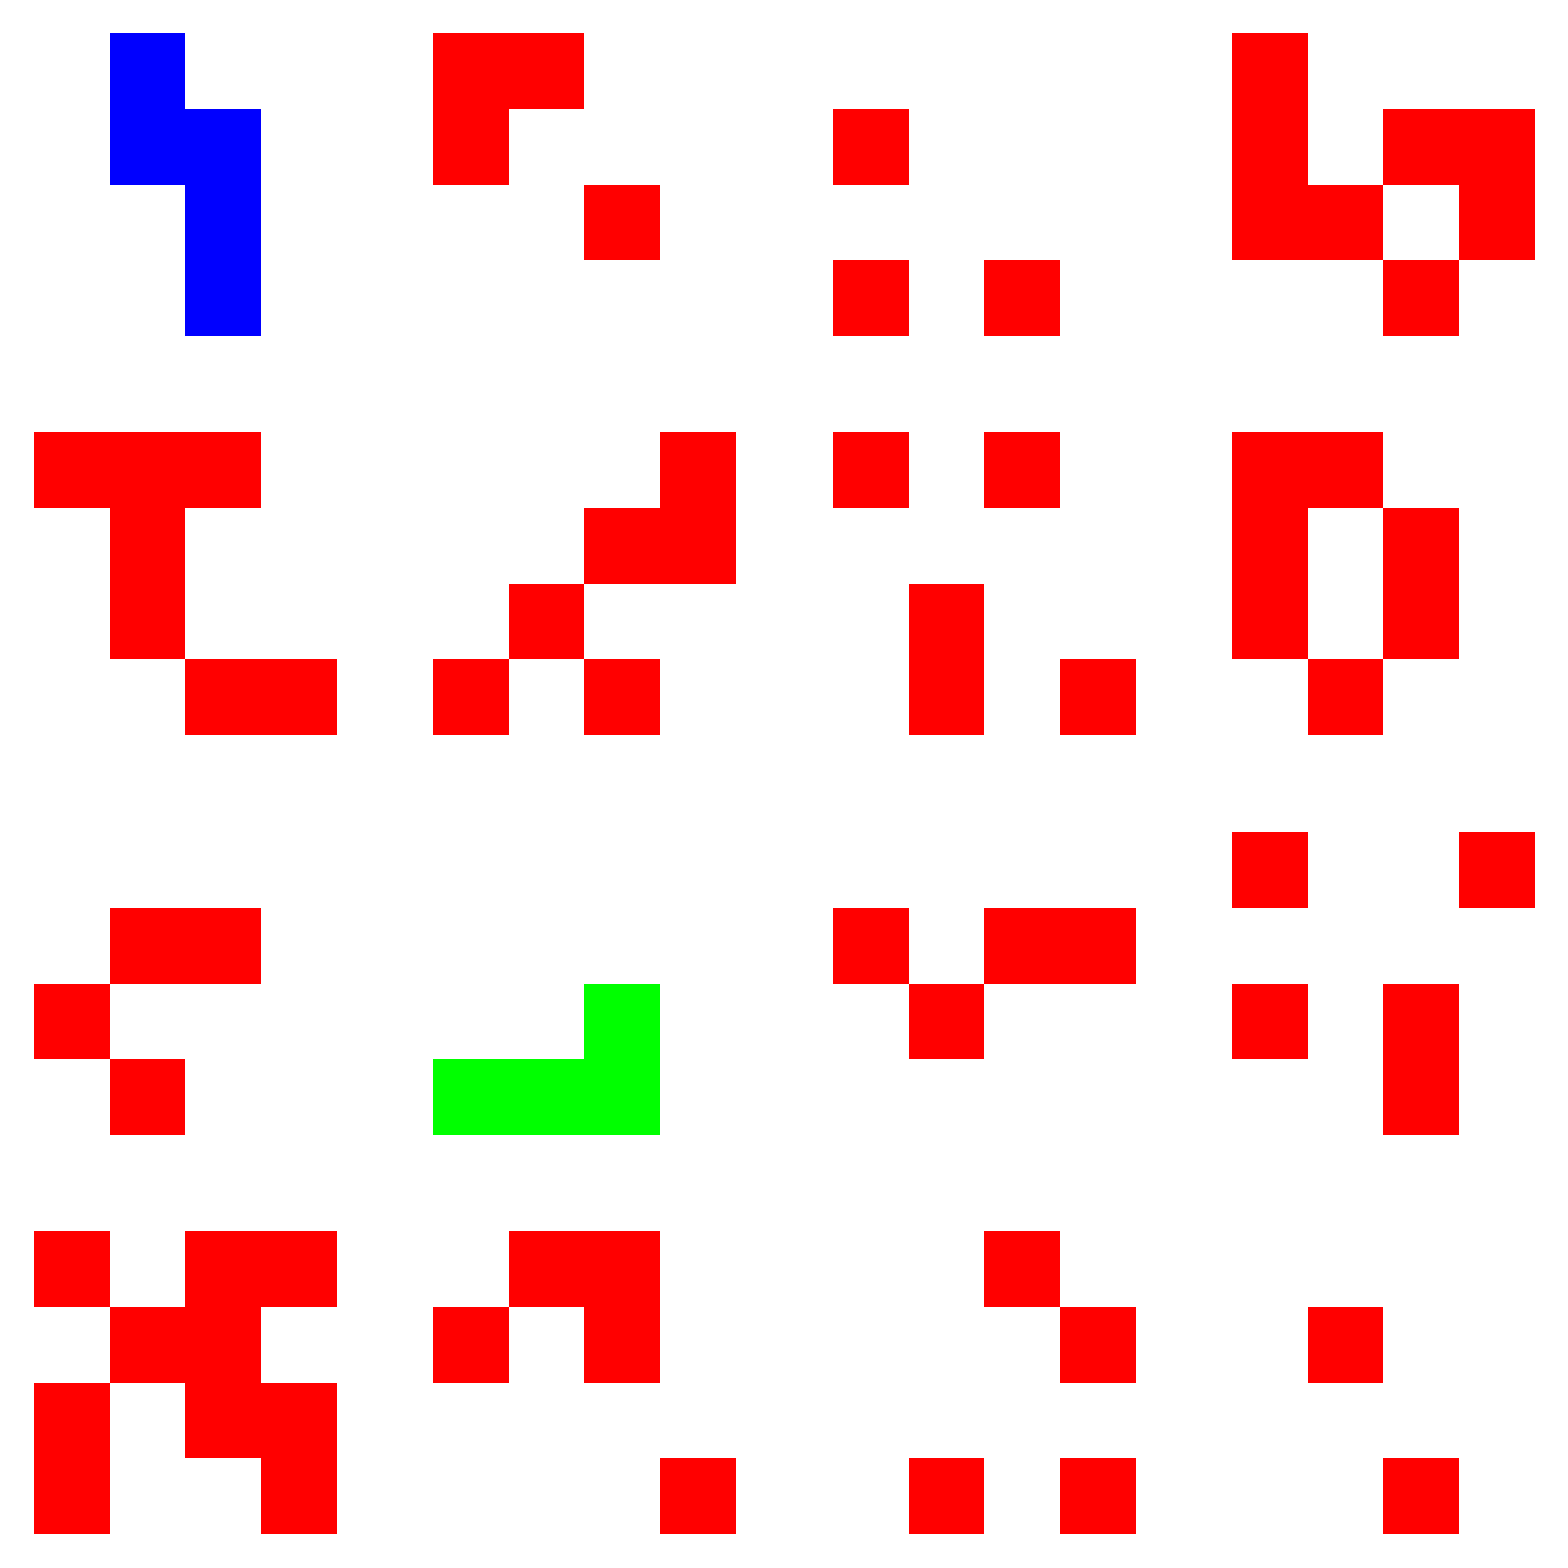

```mathematica
gFinal=Show[GraphicsGrid[{{fPlot@data,fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data]},{fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data]},{fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data]},{fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data],fPlotDataFake[data]}}]]
```

```mathematica
Export["Evaluation_bateriaPPCArray.pdf",gFinal]
```

Evaluation_bateriaPPCArray.pdf